```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 67 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,VariationalMethods`,System`,Global`}

```mathematica
Clear[r]
r = { l Sin[θ[t]] , 0 , - l Cos[θ[t] ] }
```

{l Sin[θ[t]],0,-l Cos[θ[t]]}

```mathematica
D[r, t]
```

{l Cos[θ[t]] θ'[t],0,l Sin[θ[t]] θ'[t]}

```mathematica
Clear[Φ]
Φ = {  0 , 0, ϕ[t] }
```

{0,0,ϕ[t]}

```mathematica
D[Φ, t]
```

{0,0,ϕ'[t]}

```mathematica
Clear[v]
v = D[r, t] + Cross[ D[Φ, t] , r ]
```

{l Cos[θ[t]] θ'[t],l Sin[θ[t]] ϕ'[t],l Sin[θ[t]] θ'[t]}

```mathematica
v . v
```

l^2 Cos[θ[t]]^2 θ'[t]^2+l^2 Sin[θ[t]]^2 θ'[t]^2+l^2 Sin[θ[t]]^2 ϕ'[t]^2

```mathematica
v . v // Expand  // Simplify
```

l^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Clear[T] 
T = 1/2 m ( v . v // Expand  // Simplify  )
```

1/2 l^2 m (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Clear[V]
V = m g l Cos[θ[t]]
```

g l m Cos[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V
```

-g l m Cos[θ[t]]+1/2 l^2 m (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Clear[q]
q = { θ[t] , ϕ[t] }
```

{θ[t],ϕ[t]}

```mathematica
D[q, t]
```

{θ'[t],ϕ'[t]}

```mathematica
D[D[ ℒ , D[q[[1]], t] ],t]- D[ ℒ , q[[1]] ] == 0 
D[D[ ℒ , D[q[[2]], t] ],t]- D[ ℒ , q[[2]] ] == 0
```

-g l m Sin[θ[t]]-l^2 m Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+l^2 m θ''[t]==0

2 l^2 m Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]+l^2 m Sin[θ[t]]^2 ϕ''[t]==0

```mathematica
Table[
D[D[ ℒ , D[q[[i]], t] ],t]- D[ ℒ , q[[i]] ] == 0 ,
{i,1,2}] // TableForm
```

-g l m Sin[θ[t]]-l^2 m Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+l^2 m θ''[t]==0
2 l^2 m Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]+l^2 m Sin[θ[t]]^2 ϕ''[t]==0

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

l m (g Sin[θ[t]]+l Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2-l θ''[t])==0
-l^2 m Sin[θ[t]] (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t])==0

```mathematica
Clear[ics]
ics = {
θ[0] == π/6,
θ'[0] == 0.3 ,
ϕ[0] == 0.1,
ϕ'[0] == 3 
};
ics // TableForm
```

θ[0]==π/6
θ'[0]==0.3
ϕ[0]==0.1
ϕ'[0]==3

```mathematica
Clear[parameters]
parameters = {
m-> 20 ,
g-> 9.8 ,
l-> 5 
};
parameters // TableForm
```

m→20
g→9.8
l→5

```mathematica
eqs /. parameters
```

{100 (9.8 Sin[θ[t]]+5 Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2-5 θ''[t])==0,-500 Sin[θ[t]] (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t])==0}

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[eqs /. parameters, ics] , q, {t,0,10} ]
```

{{θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}}

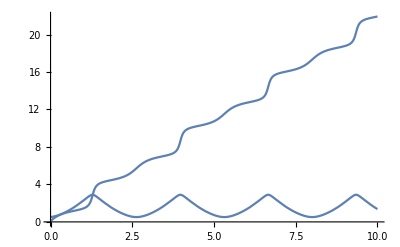

```mathematica
Plot[ q /. solution , {t,0,10} ]
```

```mathematica
Exit[]
Quit[]
```